## Figure 2 (Two species which only differ in soil and resource preference)

### Setup

```mathematica
ClearAll["α","β","f","g"]
```

```mathematica
f[ν_,σ_,ζ_]:=ν NIntegrate[Exp[(-(x+ζ)^2)/σ^2]Exp[(-(x-ζ)^4)/(81 σ^4)],{x,-Infinity,Infinity}]/NIntegrate[Exp[(-(x+ζ)^2)/σ^2]^2,{x,-Infinity,Infinity}]
```

```mathematica
g[ν_,σ_,ζ_]:=ν NIntegrate[Exp[(-(x+ζ)^2)/σ^2]Exp[(-(x+ζ)^4)/(81 σ^4)],{x,-Infinity,Infinity}]/NIntegrate[Exp[(-(x+ζ)^2)/σ^2]^2,{x,-Infinity,Infinity}]
```

#### Dynamics

```mathematica
Subscript[dN, 1]:=Subscript[N, 1](1-(S+ϵ)^4/ω^4-( β Subscript[N, 1]+α Subscript[N, 2]));
Subscript[dN, 2]:=Subscript[N, 2](1-(S-ϵ)^4/ω^4-(α Subscript[N, 1]+β Subscript[N, 2]));
dS:=η(-ϵ-S)Subscript[N, 1]+η(ϵ-S)Subscript[N, 2];
```

```mathematica
Jc={{D[Subscript[dN, 1],Subscript[N, 1]],D[Subscript[dN, 1],Subscript[N, 2]],D[Subscript[dN, 1],S]},{D[Subscript[dN, 2],Subscript[N, 1]],D[Subscript[dN, 2],Subscript[N, 2]],D[Subscript[dN, 2],S]},{D[dS,Subscript[N, 1]],D[dS,Subscript[N, 2]],D[dS,S]}};
```

#### Equilibrium

```mathematica
eqN=FullSimplify[Solve[Subscript[dN, 1]==0&&Subscript[dN, 2]==0,{Subscript[N, 1],Subscript[N, 2]}]]
```

{{N_1→0,N_2→0},{N_1→0,N_2→(-(S-ϵ)^4+ω^4)/(β ω^4)},{N_1→(S^4 (-α+β)+4 S^3 (α+β) ϵ+6 S^2 (-α+β) ϵ^2+4 S (α+β) ϵ^3+(α-β) (-ϵ^4+ω^4))/((α-β) (α+β) ω^4),N_2→(S^4 (-α+β)-4 S^3 (α+β) ϵ+6 S^2 (-α+β) ϵ^2-4 S (α+β) ϵ^3+(α-β) (-ϵ^4+ω^4))/((α-β) (α+β) ω^4)},{N_1→(-(S+ϵ)^4+ω^4)/(β ω^4),N_2→0}}

### Figure 2a (Filtering only figure with soil origin dependence)

```mathematica
ClearAll["pars"]
pars={ω->1,σ->1,ν->1,η->1,ζ->1};
```

```mathematica
figFilter=RegionPlot[{S>(ϵ-ω/.pars)&&S<(-ϵ+ω/.pars),S<(ϵ-ω/.pars)&&(-ϵ-ω/.pars)<S<(ϵ+ω/.pars),S>(-ϵ+ω/.pars)&&S<(ϵ+ω/.pars)&&S>(ϵ-ω/.pars),S<(-ϵ-ω/.pars)||S>(ϵ+ω/.pars)||(S>(-ϵ+ω/.pars)&&S<(ϵ-ω/.pars))},{S,-2.2,2.2},{ϵ,0,1.2},MaxRecursion->5,PlotStyle->{RGBColor[0.28026441037696703, 0.715, 0.4292089322474965],RGBColor[0.5016764639999998, 0.7492700575999999, 0.9393325664],RGBColor[0.9529226912, 0.93983914, 0.6205618136],LightGray},BoundaryStyle->None];
```

```mathematica
α=f[ν/.pars,σ/.pars,ζ/.pars]
β=g[ν/.pars,σ/.pars,ζ/.pars]
```

1.06713

1.40176

```mathematica
figCoex=RegionPlot[((Subscript[dN, 1]/Subscript[N, 1])/.eqN[[2]]/.pars)>0&&((Subscript[dN, 2]/Subscript[N, 2])/.eqN[[4]]/.pars)>0,{S,-1.1,1.2},{ϵ,0,1.2},MaxRecursion->8,PlotStyle->None,BoundaryStyle->Red];
```

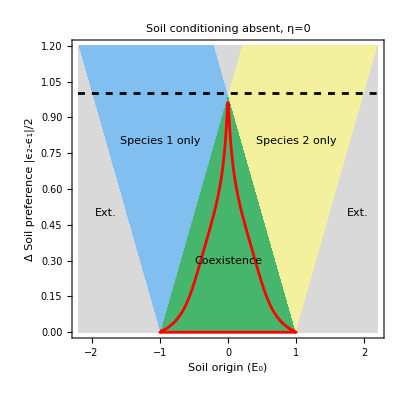

```mathematica
fig2a=Show[{figFilter,figCoex,Plot[ω/.pars,{S,-2.2,2.2},PlotStyle->{Dashed,Black}]},Frame->True,FrameLabel->{"Soil origin (E_0)","Δ Soil preference |ϵ_2-ϵ_1|/2"},LabelStyle->{FontSize->20,FontColor->Black},PlotLabel->Style["Soil conditioning absent, η=0",FontSize->20],AspectRatio->1,Epilog->{Inset[Text[Style["Species 1 only ",FontSize->15]],{-1,0.8}],Inset[Text[Style["Coexistence ",FontSize->15]],{0,0.3}],Inset[Text[Style["Species 2 only ",FontSize->15]],{1,0.8}],Inset[Text[Style["Ext. ",FontSize->15]],{-1.8,0.5}],Inset[Text[Style["Ext. ",FontSize->15]],{1.9,0.5}]}]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\fig2a.jpg",fig2a];
```

### Figure 2b (PSF and competition figure with soil origin dependence)

```mathematica
ClearAll["pars"]
pars={ω->1,σ->1,ν->1,η->1,ζ->1};
α=f[ν/.pars,σ/.pars,ζ/.pars]
β=g[ν/.pars,σ/.pars,ζ/.pars]
```

1.06713

1.40176

```mathematica
ϵs =Range[0,1.2,0.01];
nϵ = Length[ϵs];
Ss = Range[-2.2, 2.2, 0.05];
nS = Length[Ss];
```

```mathematica
ClearAll["xf","yf","zf"]
```

```mathematica
xf=Array[,{nϵ*nS,3}];
yf=Array[,{nϵ*nS,3}];
yf1=Array[,{nϵ*nS,3}];
yf2=Array[,{nϵ*nS,3}];
yf3=Array[,{nϵ*nS,3}];
zf=Array[,{nϵ*nS,3}];
st=Array[,{nϵ*nS,3}];
```

```mathematica
x0=0.1;y0=0.1; T=1000; 
dx=Subscript[dN, 1]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dy=Subscript[dN, 2]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dz=dS/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
```

```mathematica
DOPRIamat={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DOPRIbvec={35/384,0,500/1113,125/192,-2187/6784,11/84,0};
DOPRIcvec={1/5,3/10,4/5,8/9,1,1};
DOPRIevec={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};
DOPRICoefficients[5,p_]:=N[{DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec},p];
```

```mathematica
Timing[
Do[
Do[
nsol=NDSolve[{D[x[t],t]==(dx/.ϵ->ϵs[[j2]]),D[y[t],t]==(dy/.ϵ->ϵs[[j2]]),D[z[t],t]==(dz/.ϵ->ϵs[[j2]]),x[0]==x0,y[0]==y0,z[0]==Ss[[j1]]},{x,y,z},{t,0,T},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
If[Extract[x[T]/.nsol,1]<-0.001||Extract[y[T]/.nsol,1]<-0.001,
Print[{(x[T]/.nsol),(y[T]/.nsol),Ss[[j1]],ϵs[[j2]]}],
xf[[(j1-1)*nϵ+j2]]=Flatten[{Ss[[j1]],ϵs[[j2]],x[T]/.nsol}];
yf[[(j1-1)*nϵ+j2]]=Flatten[{Ss[[j1]],ϵs[[j2]],y[T]/.nsol}];
zf[[(j1-1)*nϵ+j2]]=Flatten[{Ss[[j1]],ϵs[[j2]],z[T]/.nsol}];
If[Extract[x[T]/.nsol,1]>0.1&&Extract[y[T]/.nsol,1]>0.1,st[[(j1-1)*nϵ+j2]]={Ss[[j1]],ϵs[[j2]],0}];
If[Extract[x[T]/.nsol,1]>0.1&&Extract[y[T]/.nsol,1]<0.1,st[[(j1-1)*nϵ+j2]]={Ss[[j1]],ϵs[[j2]],1}];
If[Extract[x[T]/.nsol,1]<0.1&&Extract[y[T]/.nsol,1]>0.1,st[[(j1-1)*nϵ+j2]]={Ss[[j1]],ϵs[[j2]],2}];
If[Extract[x[T]/.nsol,1]<0.1&&Extract[y[T]/.nsol,1]<0.1,st[[(j1-1)*nϵ+j2]]={Ss[[j1]],ϵs[[j2]],3}];
],
{j2,nϵ}],
{j1,nS}]
]
```

{158.938,Null}

```mathematica
myColor[z_]:=Piecewise[{{RGBColor[0.28026441037696703, 0.715, 0.4292089322474965],0<=z<1},{RGBColor[0.5016764639999998, 0.7492700575999999, 0.9393325664],1<=z<2},{RGBColor[0.9529226912, 0.93983914, 0.6205618136],2<=z<3},{LightGray,z>=3}}]
```

```mathematica
figPSF=ListDensityPlot[st,ColorFunctionScaling->False,ColorFunction->myColor,Frame->True,FrameLabel->{"",""},LabelStyle->{FontSize->15,FontColor->Black}];
```

```mathematica
fig2b=Show[{figPSF,figCoex,Plot[ω/.pars,{x,-2.2,2.2},PlotStyle->{Dashed,Black}]},Frame->True,FrameLabel->{"Soil origin (E_0)","Δ Soil preference |ϵ_2-ϵ_1|/2"},LabelStyle->{FontSize->20,FontColor->Black},PlotRange->{{-2.2,2.2},{0,1.2}},PlotLabel->Style["Soil conditioning present, η=1",FontSize->20],Epilog-> {Inset[Text[Style["Species 1 only ",FontSize->15]],{-1,0.8}],Inset[Text[Style["Coexistence ",FontSize->15]],{0,0.3}],Inset[Text[Style["Species 2 only ",FontSize->15]],{1,0.8}],Inset[Text[Style["Ext. ",FontSize->15]],{-1.85,0.4}],Inset[Text[Style["Ext. ",FontSize->15]],{1.95,0.4}]}]
```

-Graphics-

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\fig2b_part.jpg",fig2b,ImageResolution->500];
```

### Figure 2c (Coexistence and priority effects with PSF)

```mathematica
pars={ω->1,σ->1,ν->1,η->1};
ϵs=Range[0,0.7,0.01];
nϵ=Length[ϵs];
ζs=Range[0,3,0.05];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
z4=Array[,{nζ,2}];
z5=Array[,{nζ,2}];
z6=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
```

```mathematica
eqCounts=List[0,0,0,0,0,0];
```

```mathematica
Do[
ch1=0;
ch2=0;
Do[
α=f[ν/.pars,σ/.pars,ζs[[j1]]];
β=g[ν/.pars,σ/.pars,ζs[[j1]]];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];
If[Length[eq[[j1,j2]]]==3,
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]];
If[Length[eq[[j1,j2]]]==1,
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]];
λ2[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1/β,Subscript[N, 2]->0,S->-ϵs[[j2]]}]];
λ3[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1/β,S->ϵs[[j2]]}]];

eqCounts[[Length[eq[[j1,j2]]]+1]]++;

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]≥0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ2[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]<0&&λ3[[j1,j2]]<0&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1],

{j2,nϵ}],
{j1,nζ}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Eigenvalues::eival: Unable to find all roots of the characteristic polynomial.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)

```mathematica
eqCounts
```

{0,3666,0,665,0,0}

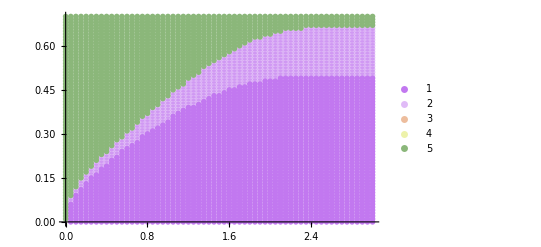

```mathematica
ListPlot[{y1,y2,y3,y4,y5},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]}}]
```

```mathematica
f1=Interpolation[z1];
f2=Interpolation[z2];
```

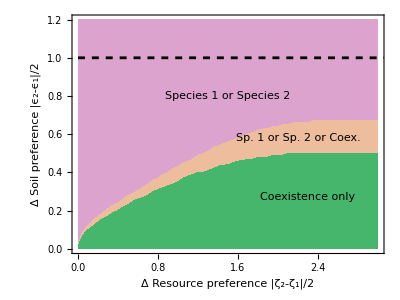

```mathematica
fig2c=Show[{RegionPlot[{y>f2[x],y<f2[x],y<f1[x]},{x,0,3},{y,0,1.2},PlotStyle->{RGBColor[0.8570441666666667, 0.6373188333333333, 0.8020406666666666],RGBColor[0.927848, 0.742785, 0.6151383333333333],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]},BoundaryStyle->None],Plot[ω/.pars,{ζ,0,6},PlotStyle->{Dashed,Black}]},Frame->True,FrameLabel->{"Δ Resource preference |ζ_2-ζ_1|/2","Δ Soil preference |ϵ_2-ϵ_1|/2"},Axes->{False,False},LabelStyle->{FontSize->18,FontColor->Black},Epilog-> {{Inset[Text[Style["Species 1 or Species 2",FontSize->15]],{1.5,0.8}],Inset[Text[Style["Sp. 1 or Sp. 2 or Coex. ",FontSize->15]],{2.2,0.58}],Inset[Text[Style["Coexistence only ",FontSize->15]],{2.3,0.27}]}},AspectRatio->0.75]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\fig2c.jpg",fig2c];
```

```mathematica
ζs[[41]]
```

2.

```mathematica
ϵ1Fix=z1[[41,2]]
ϵ2Fix=z2[[41,2]]
```

0.49

0.64

## Numerics

```mathematica
pars={ω->1,σ->1,ν->1,η->1,ζ->2.35,ϵ->0.5};
```

```mathematica
α=f[ν/.pars,σ/.pars,ζ/.pars]
```

0.0381196

```mathematica
x0=1;y0=2;z0=0; T=10000; 
dx=Subscript[dN, 1]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dy=Subscript[dN, 2]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dz=dS/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
```

```mathematica
nsol=NDSolve[{D[x[t],t]==dx,D[y[t],t]==dy,D[z[t],t]==dz,x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,0,T}];
```

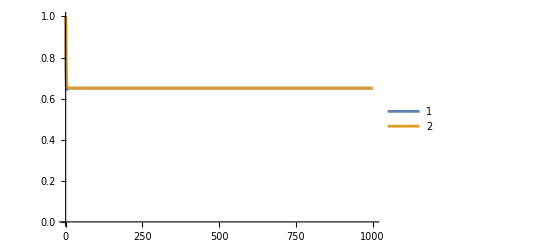

```mathematica
Plot[{x[t]/.nsol,y[t]/.nsol},{t,0,1000},PlotRange->{0,1},PlotLegends->Automatic,Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}]
```

```mathematica
eqNSol=FullSimplify[Solve[N[Subscript[dN, 1]/.pars]==0&&N[Subscript[dN, 2]/.pars]==0&&N[dS/.pars]==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{N_1→0.00666668,N_2→0.713206,S→0.490739},{N_1→0.651095,N_2→0.651095,S→0},{N_1→0.713206,N_2→0.00666668,S→-0.490739}}

```mathematica
Eigenvalues[Jc/.pars/.eqNSol[[1]]]
```

{-0.999728,-0.754391,0.0251555}

```mathematica
Eigenvalues[Jc/.pars/.Subscript[N, 1]->1/.Subscript[N, 2]->0/.S->0]
```

{-2.09445,0.89938,-0.771575}

```mathematica
Eigenvalues[Jc/.pars/.Subscript[N, 1]->0/.Subscript[N, 2]->1/.S->0.5]
```

{-1.80353,-1.,-0.0381196}